```mathematica
Clear[phystest];
Clear[zero];
Clear[Σ];
Clear[s];
Clear[d];
Clear[g];
Clear[λ];
Clear[a];
Clear[b];
Clear[cp];
Clear[cm];
Clear[covm];
```

```mathematica
zero={{0,0},{0,0}};
```

```mathematica
Σ=ArrayFlatten[{{ⅈ PauliMatrix[2],zero},{zero,ⅈ PauliMatrix[2]}}];
```

(A | Cc
Cc | B)

```mathematica
s=Table[RandomReal[{1,100}],{i,10^3}];
d=Table[RandomReal[{0,s[[i]]-1}],{i,10^3}];
g=Table[RandomReal[{2 Abs[d[[i]]]+1,2s[[i]]-1}],{i,10^3}];
λ=Table[RandomReal[{-1,1}],{i,10^3}];

a=Table[s[[i]]+d[[i]],{i,10^3}];

b=Table[s[[i]]-d[[i]],{i,10^3}];


cp=Table[
1/(4 √(s[[i]]^2-d[[i]]^2))*(√((4 d[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2)+√((4 s[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2))
,{i,10^3}]//FullSimplify;

cm=Table[
1/(4 √(s[[i]]^2-d[[i]]^2))*(√((4 d[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2)-√((4 s[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2))
,{i,10^3}]//FullSimplify;
```

```mathematica
cp[[1]]
```

38.0073

```mathematica
covm=Table[{{a[[i]],0,cp[[i]],0},{0,a[[i]],0,cm[[i]]},{cp[[i]],0,b[[i]],0},{0,cm[[i]],0,b[[i]]}},{i,10^3}];
```

```mathematica
covm[[4]]
```

{{129.908,0,56.1296,0},{0,129.908,0,-34.4913},{56.1296,0,24.3055,0},{0,-34.4913,0,24.3055}}

{{9.05891,0,-1.80664,0},{0,9.05891,0,-3.84297},{-1.80664,0,5.39379,0},{0,-3.84297,0,5.39379}}

```mathematica
Clear[phystest]
```

```mathematica
phystest={};
Do[AppendTo[phystest,{Eigenvalues[covm[[i]]],Eigenvalues[covm[[i]]+ⅈ Σ],Abs[Eigenvalues[ⅈ Σ . covm[[i]]//Chop]]}];,{i,1,Length[covm]}]
```

```mathematica
Length[phystest]
```

1000

```mathematica
phystest[[200]]
```

{{169.783,141.908,27.8978,0.0228131},{169.793,141.91,27.8953,0.0127478},{82.2452,82.2452,1.50562,1.50562}}

```mathematica
{1,Min[phystest[[1,1]]]}
```

{1,0.0404235}

```mathematica
Table[{i,Min[phystest[[i,1]]]},{i,1,Length[cm]}]
```

{{1,0.0404235},{2,0.0260425},{3,0.0511437},{4,0.0451079},{5,0.365979},{6,0.0260979},{7,0.0498877},{8,0.013781},{9,0.140864},{10,0.0315416},{11,0.030678},{12,0.0404494},{13,0.197747},{14,0.0333411},{15,0.0325412},{16,0.0102585},{17,0.149084},{18,0.0718614},{19,0.488383},{20,0.0486127},{21,0.807149},{22,0.381161},{23,0.4635},{24,0.102065},{25,0.0399483},{26,0.331574},{27,0.00967872},{28,0.0219576},{29,0.461874},{30,0.15396},{31,0.342013},{32,0.0504635},{33,0.068199},{34,0.131045},{35,0.0132854},{36,0.0817199},{37,0.120893},{38,0.569216},{39,0.189969},{40,0.0336016},{41,0.0580837},{42,0.0178247},{43,0.57698},{44,0.467313},{45,0.699186},{46,0.0433842},{47,0.136335},{48,0.386189},{49,0.345766},{50,0.0150789},{51,0.0315692},{52,0.0186359},{53,0.274809},{54,0.504204},{55,0.141144},{56,0.103719},{57,0.233514},{58,0.336217},{59,0.176096},{60,0.492579},{61,0.0525661},{62,0.0421184},{63,0.425542},{64,0.0351499},{65,0.139407},{66,0.0690447},{67,0.0487266},{68,0.181906},{69,0.116489},{70,0.129539},{71,0.0430565},{72,0.529176},{73,0.0241286},{74,0.0439662},{75,0.00788225},{76,0.0441257},{77,0.183288},{78,0.544067},{79,0.0463685},{80,0.067829},{81,0.780462},{82,0.0450242},{83,0.0159969},{84,0.0583947},{85,0.134158},{86,0.0871631},{87,0.0316094},{88,0.277753},{89,0.0795459},{90,0.0100569},{91,0.0166761},{92,0.0960732},{93,0.337644},{94,0.0180725},{95,0.0552499},{96,0.152481},{97,0.241716},{98,0.851049},{99,0.282068},{100,0.0477491},{101,0.0109967},{102,0.0321474},{103,0.375977},{104,0.0722961},{105,0.0111569},{106,0.197228},{107,0.0496512},{108,0.13476},{109,0.277194},{110,0.0521737},{111,0.376271},{112,0.743255},{113,0.936175},{114,0.0159032},{115,0.15636},{116,0.0245129},{117,0.0654826},{118,0.164043},{119,0.0139019},{120,0.0227914},{121,0.0880565},{122,0.015926},{123,0.325124},{124,0.0303521},{125,0.0259261},{126,0.103694},{127,0.267187},{128,0.0311073},{129,0.179233},{130,0.0177524},{131,0.0612147},{132,0.0919992},{133,0.399007},{134,0.173248},{135,0.217023},{136,0.0432476},{137,0.0524075},{138,0.231863},{139,0.0115272},{140,0.0184034},{141,0.848389},{142,0.494879},{143,0.0852454},{144,0.0645472},{145,0.186547},{146,0.256323},{147,0.0268746},{148,0.608691},{149,0.30195},{150,0.0306166},{151,0.0162601},{152,0.0670375},{153,0.0468027},{154,0.0185891},{155,0.686367},{156,0.12719},{157,0.352926},{158,0.140552},{159,0.0424745},{160,0.734856},{161,0.311814},{162,0.0324195},{163,0.795824},{164,0.0616218},{165,0.0460356},{166,0.103595},{167,0.0520729},{168,0.124145},{169,0.028199},{170,0.0977573},{171,0.0923767},{172,0.0491634},{173,0.278016},{174,0.0550219},{175,0.0325982},{176,0.412043},{177,0.270746},{178,0.116667},{179,0.017851},{180,0.20699},{181,0.135696},{182,0.259314},{183,0.223497},{184,0.126957},{185,0.127334},{186,0.186828},{187,0.710207},{188,0.0267297},{189,0.03024},{190,0.113347},{191,0.115489},{192,0.207451},{193,0.068168},{194,0.032932},{195,0.0832308},{196,0.0247153},{197,0.19453},{198,0.109288},{199,0.135281},{200,0.0228131},{201,0.0632076},{202,0.046035},{203,0.0432808},{204,0.0440236},{205,0.107061},{206,0.170419},{207,0.0633382},{208,0.10336},{209,0.794024},{210,0.272464},{211,0.0484514},{212,0.0784058},{213,0.0314976},{214,0.0517698},{215,0.634331},{216,0.297324},{217,0.385659},{218,0.535535},{219,0.551754},{220,0.0604654},{221,0.0558755},{222,0.243383},{223,0.840576},{224,0.0666784},{225,0.224282},{226,0.0684699},{227,0.0527975},{228,0.383049},{229,0.0743603},{230,0.0331994},{231,0.0662138},{232,0.0551802},{233,0.0494157},{234,0.128964},{235,0.0479452},{236,0.190134},{237,0.049086},{238,0.270485},{239,0.28995},{240,0.0116372},{241,0.113081},{242,0.111146},{243,0.0450713},{244,0.627979},{245,0.0501431},{246,0.906549},{247,0.140345},{248,0.291237},{249,0.370593},{250,0.0374744},{251,0.0128427},{252,0.0557723},{253,0.0762793},{254,0.272327},{255,0.0393051},{256,0.0753276},{257,0.0694249},{258,0.0246266},{259,0.0298312},{260,0.0102802},{261,0.0854981},{262,0.162947},{263,0.0129684},{264,0.0525484},{265,0.0230179},{266,0.0998776},{267,0.549789},{268,0.264892},{269,0.0372827},{270,0.045437},{271,0.101663},{272,0.0296616},{273,0.0476253},{274,0.141137},{275,0.144855},{276,0.0465176},{277,0.109179},{278,0.2445},{279,0.0426772},{280,0.0576253},{281,0.247001},{282,0.0506716},{283,0.133248},{284,0.0808828},{285,0.132302},{286,0.320978},{287,0.0962669},{288,0.155161},{289,0.0812761},{290,0.193312},{291,0.154391},{292,0.086543},{293,0.221959},{294,0.0186898},{295,0.0640903},{296,0.162884},{297,0.0217467},{298,0.0228202},{299,0.0117914},{300,0.0625959},{301,0.166984},{302,0.302434},{303,0.0223144},{304,0.0955712},{305,0.0742949},{306,0.129915},{307,0.0658957},{308,0.13249},{309,0.521344},{310,0.0685977},{311,0.0245017},{312,0.262549},{313,0.374357},{314,0.0318357},{315,0.0824297},{316,0.0280078},{317,0.0728451},{318,0.173961},{319,0.0501533},{320,0.168813},{321,0.0292809},{322,0.159381},{323,0.419732},{324,0.256624},{325,0.222347},{326,0.0451701},{327,0.115454},{328,0.0313086},{329,0.535396},{330,0.00983395},{331,0.0668406},{332,0.186402},{333,0.142834},{334,0.00775311},{335,0.0151382},{336,0.0841392},{337,0.0110474},{338,0.245409},{339,0.0361129},{340,0.187614},{341,0.796051},{342,0.0459654},{343,0.126201},{344,0.273921},{345,0.0567636},{346,0.0899995},{347,0.10237},{348,0.377323},{349,0.25815},{350,0.0648377},{351,0.0563248},{352,0.365602},{353,0.0691364},{354,0.170058},{355,0.0499164},{356,0.0480208},{357,0.0405969},{358,0.0569233},{359,0.0212457},{360,0.0744285},{361,0.0190383},{362,0.205829},{363,0.0203997},{364,0.305133},{365,0.0287186},{366,0.0712867},{367,0.0558871},{368,0.0504961},{369,0.948523},{370,0.132804},{371,0.0260395},{372,0.113233},{373,0.0505407},{374,0.0271194},{375,0.112915},{376,0.164402},{377,0.46568},{378,0.036729},{379,0.00814103},{380,0.151575},{381,0.027994},{382,0.376281},{383,0.155728},{384,0.0188131},{385,0.0867024},{386,0.0184479},{387,0.0387866},{388,0.208814},{389,0.239709},{390,0.0611317},{391,0.0101323},{392,0.573362},{393,0.371497},{394,0.231762},{395,0.077567},{396,0.115569},{397,0.022592},{398,0.561886},{399,0.474653},{400,0.158064},{401,0.369557},{402,0.237537},{403,0.516208},{404,0.0287365},{405,0.0212612},{406,0.0444764},{407,0.34468},{408,0.0107002},{409,0.0373011},{410,0.143579},{411,0.0317964},{412,0.0925134},{413,0.0264318},{414,0.0655744},{415,0.0622282},{416,0.0239592},{417,0.0284674},{418,0.061859},{419,0.440996},{420,0.067217},{421,0.0252371},{422,0.060474},{423,0.0513203},{424,0.341932},{425,0.0197829},{426,0.0172059},{427,0.296036},{428,0.264109},{429,0.154487},{430,0.294061},{431,0.0803114},{432,0.0219059},{433,0.80757},{434,0.0282592},{435,0.0864618},{436,0.107513},{437,0.0263834},{438,0.0145221},{439,0.0891325},{440,0.284835},{441,0.0564594},{442,0.10104},{443,0.0272874},{444,0.0283592},{445,0.0550589},{446,0.0812923},{447,0.13064},{448,0.0831055},{449,0.0115832},{450,0.0472334},{451,0.100832},{452,0.564503},{453,0.0137105},{454,0.839057},{455,0.0662766},{456,0.186618},{457,0.472972},{458,0.642944},{459,0.0377807},{460,0.108217},{461,0.0320629},{462,0.266462},{463,0.321139},{464,0.039212},{465,0.0165207},{466,0.146086},{467,0.14142},{468,0.0376266},{469,0.250003},{470,0.735722},{471,0.0227174},{472,0.0834847},{473,0.207329},{474,0.0810565},{475,0.0225805},{476,0.22781},{477,0.0298642},{478,0.0623384},{479,0.91306},{480,0.00852683},{481,0.52387},{482,0.0423572},{483,0.0860289},{484,0.0817275},{485,0.053505},{486,0.0428274},{487,0.0437873},{488,0.0773223},{489,0.148009},{490,0.24246},{491,0.0324624},{492,0.0759743},{493,0.265676},{494,0.0210167},{495,0.209383},{496,0.0583797},{497,0.0459459},{498,0.111931},{499,0.783629},{500,0.0989909},{501,0.0500366},{502,0.0143702},{503,0.995877},{504,0.1586},{505,0.6453},{506,0.032817},{507,0.0417133},{508,0.429141},{509,0.0296094},{510,0.112659},{511,0.01883},{512,0.598758},{513,0.0782982},{514,0.498858},{515,0.00792389},{516,0.0323862},{517,0.0870587},{518,0.020391},{519,0.212028},{520,0.389922},{521,0.0457724},{522,0.142164},{523,0.301336},{524,0.208662},{525,0.153339},{526,0.138404},{527,0.029419},{528,0.0771285},{529,0.0340932},{530,0.456666},{531,0.0355295},{532,0.0513649},{533,0.0494457},{534,0.0429439},{535,0.0823213},{536,0.379521},{537,0.0966038},{538,0.0430795},{539,0.259905},{540,0.049837},{541,0.091723},{542,0.721829},{543,0.0912115},{544,0.0628245},{545,0.117809},{546,0.115799},{547,0.023928},{548,0.814266},{549,0.0194516},{550,0.446099},{551,0.0215122},{552,0.188301},{553,0.0359021},{554,0.44278},{555,0.500636},{556,0.257079},{557,0.0594235},{558,0.0592444},{559,0.76059},{560,0.523501},{561,0.123067},{562,0.112693},{563,0.0810927},{564,0.0284528},{565,0.0960078},{566,0.32266},{567,0.251686},{568,0.0348801},{569,0.416902},{570,0.055044},{571,0.0690251},{572,0.129991},{573,0.737952},{574,0.210765},{575,0.0487989},{576,0.113222},{577,0.0788123},{578,0.0177455},{579,0.111362},{580,0.0332418},{581,0.0367753},{582,0.703884},{583,0.25501},{584,0.048795},{585,0.755839},{586,0.037861},{587,0.127993},{588,0.042718},{589,0.0216682},{590,0.236991},{591,0.0389595},{592,0.556769},{593,0.200707},{594,0.0744854},{595,0.0585214},{596,0.0135427},{597,0.0269408},{598,0.0246846},{599,0.171501},{600,0.145211},{601,0.0376488},{602,0.0652765},{603,0.0270185},{604,0.0381532},{605,0.436685},{606,0.320771},{607,0.795466},{608,0.126132},{609,0.0251643},{610,0.0331283},{611,0.0260012},{612,0.089529},{613,0.219185},{614,0.156259},{615,0.0497012},{616,0.0533234},{617,0.597732},{618,0.25752},{619,0.343448},{620,0.539691},{621,0.25243},{622,0.0628694},{623,0.0294775},{624,0.45721},{625,0.258602},{626,0.0131218},{627,0.0812277},{628,0.0222511},{629,0.333355},{630,0.150113},{631,0.633353},{632,0.190673},{633,0.0340245},{634,0.0654278},{635,0.51013},{636,0.0346439},{637,0.130273},{638,0.0350706},{639,0.152472},{640,0.0471034},{641,0.163486},{642,0.367997},{643,0.0814022},{644,0.0331071},{645,0.193229},{646,0.0770567},{647,0.104071},{648,0.0582242},{649,0.0581707},{650,0.235964},{651,0.039947},{652,0.090067},{653,0.0347739},{654,0.0211491},{655,0.0281129},{656,0.459405},{657,0.705592},{658,0.0710596},{659,0.874696},{660,0.0259522},{661,0.0488242},{662,0.49428},{663,0.0408871},{664,0.060716},{665,0.0157413},{666,0.264978},{667,0.0369549},{668,0.825703},{669,0.0182302},{670,0.0865829},{671,0.0214736},{672,0.0261581},{673,0.0450685},{674,0.0244567},{675,0.00775537},{676,0.195814},{677,0.728252},{678,0.0292198},{679,0.0559615},{680,0.324791},{681,0.00877439},{682,0.137069},{683,0.542136},{684,0.33282},{685,0.119922},{686,0.421097},{687,0.285732},{688,0.0139461},{689,0.0261946},{690,0.0163583},{691,0.0276047},{692,0.0796365},{693,0.0289059},{694,0.0646983},{695,0.208424},{696,0.134081},{697,0.647847},{698,0.0217478},{699,0.0155795},{700,0.0158842},{701,0.0120866},{702,0.186388},{703,0.226908},{704,0.0167115},{705,0.273287},{706,0.0347536},{707,0.939858},{708,0.075025},{709,0.637052},{710,0.499879},{711,0.0207458},{712,0.244037},{713,0.599074},{714,0.259629},{715,0.274627},{716,0.0126027},{717,0.251297},{718,0.0115933},{719,0.0613076},{720,0.0910494},{721,0.82031},{722,0.524634},{723,0.4437},{724,0.0278946},{725,0.0385278},{726,0.260802},{727,0.450561},{728,0.0173264},{729,0.0353824},{730,0.0603026},{731,0.0261246},{732,0.0722933},{733,0.0413219},{734,0.0399585},{735,0.0793838},{736,0.0830539},{737,0.474091},{738,0.152966},{739,0.188374},{740,0.55792},{741,0.323722},{742,0.298243},{743,0.0508151},{744,0.451947},{745,0.043932},{746,0.0604764},{747,0.0402449},{748,0.865926},{749,0.314552},{750,0.192729},{751,0.150042},{752,0.0298312},{753,0.106909},{754,0.400799},{755,0.0687742},{756,0.362281},{757,0.0545009},{758,0.601389},{759,0.227697},{760,0.0983459},{761,0.138265},{762,0.175653},{763,0.316749},{764,0.119016},{765,0.484489},{766,0.0607384},{767,0.00816276},{768,0.0438291},{769,0.870087},{770,0.0625867},{771,0.53343},{772,0.403041},{773,0.0750848},{774,0.0170485},{775,0.134035},{776,0.079921},{777,0.0927545},{778,0.161987},{779,0.374564},{780,0.148579},{781,0.0514691},{782,0.229192},{783,0.0283382},{784,0.0303481},{785,0.196392},{786,0.0342653},{787,0.0596535},{788,0.407539},{789,0.0498571},{790,0.681269},{791,0.399882},{792,0.168305},{793,0.0374427},{794,0.0229665},{795,0.204683},{796,0.0890201},{797,0.335127},{798,0.0275348},{799,0.033124},{800,0.032371},{801,0.0397744},{802,0.0576966},{803,0.399809},{804,0.299159},{805,0.343674},{806,0.0162416},{807,0.0317894},{808,0.281175},{809,0.597362},{810,0.0650786},{811,0.154335},{812,0.360591},{813,0.0923196},{814,0.526983},{815,0.572761},{816,0.774696},{817,0.200539},{818,0.0879234},{819,0.0442218},{820,0.128985},{821,0.0689793},{822,0.568869},{823,0.0537846},{824,0.0858844},{825,0.394487},{826,0.106777},{827,0.427769},{828,0.0268836},{829,0.0940543},{830,0.0703976},{831,0.142871},{832,0.0330037},{833,0.0567631},{834,0.0314979},{835,0.205229},{836,0.35177},{837,0.269671},{838,0.00939165},{839,0.53975},{840,0.201302},{841,0.0432927},{842,0.133907},{843,0.0343338},{844,0.089904},{845,0.414391},{846,0.0378871},{847,0.0305144},{848,0.180402},{849,0.365923},{850,0.457724},{851,0.0484198},{852,0.021419},{853,0.147238},{854,0.0469951},{855,0.193616},{856,0.0606938},{857,0.100458},{858,0.0502821},{859,0.124157},{860,0.0450958},{861,0.154478},{862,0.0597902},{863,0.0372404},{864,0.041821},{865,0.157488},{866,0.0255906},{867,0.102071},{868,0.237949},{869,0.312464},{870,0.0300825},{871,0.0462798},{872,0.24392},{873,0.406757},{874,0.293036},{875,0.54352},{876,0.983749},{877,0.0258671},{878,0.0452747},{879,0.0736049},{880,0.0564898},{881,0.391344},{882,0.0385435},{883,0.0285953},{884,0.713376},{885,0.145853},{886,0.00656627},{887,0.0294536},{888,0.0446306},{889,0.0670033},{890,0.289039},{891,0.175134},{892,0.0383954},{893,0.0825632},{894,0.0365936},{895,0.0944092},{896,0.0711761},{897,0.173516},{898,0.311675},{899,0.206897},{900,0.194248},{901,0.00716708},{902,0.0879504},{903,0.404257},{904,0.0255481},{905,0.0781746},{906,0.195357},{907,0.120389},{908,0.118798},{909,0.159848},{910,0.0341879},{911,0.0929836},{912,0.244568},{913,0.156007},{914,0.0275231},{915,0.0223976},{916,0.868016},{917,0.103636},{918,0.475414},{919,0.18612},{920,0.0835732},{921,0.309211},{922,0.151855},{923,0.0375642},{924,0.0921384},{925,0.0486558},{926,0.0495296},{927,0.0232292},{928,0.0636053},{929,0.0449584},{930,0.603641},{931,0.0272261},{932,0.0819268},{933,0.0107531},{934,0.121059},{935,0.512937},{936,0.0144493},{937,0.0147445},{938,0.0343086},{939,0.0205517},{940,0.387277},{941,0.0539843},{942,0.0639963},{943,0.313457},{944,0.0471417},{945,0.0407847},{946,0.0187898},{947,0.186271},{948,0.22666},{949,0.412294},{950,0.0373928},{951,0.0637315},{952,0.604715},{953,0.106458},{954,0.208902},{955,0.0231237},{956,0.105846},{957,0.0407886},{958,0.0359266},{959,0.338716},{960,0.125956},{961,0.064336},{962,0.0146346},{963,0.171911},{964,0.0406303},{965,0.160028},{966,0.137356},{967,0.171211},{968,0.102697},{969,0.125513},{970,0.106432},{971,0.0227523},{972,0.0287855},{973,0.228625},{974,0.717876},{975,0.0352497},{976,0.249007},{977,0.159902},{978,0.783651},{979,0.0319925},{980,0.101685},{981,0.368965},{982,0.816988},{983,0.21859},{984,0.09035},{985,0.0345937},{986,0.635803},{987,0.138539},{988,0.080726},{989,0.256198},{990,0.0799671},{991,0.0853356},{992,0.0524173},{993,0.137808},{994,0.109669},{995,0.0139696},{996,0.0336848},{997,0.19497},{998,0.141696},{999,0.0604743},{1000,0.0136771}}

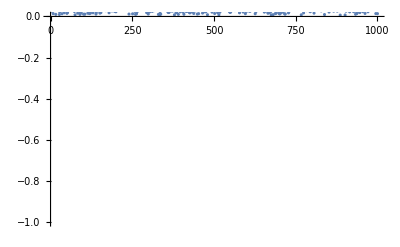

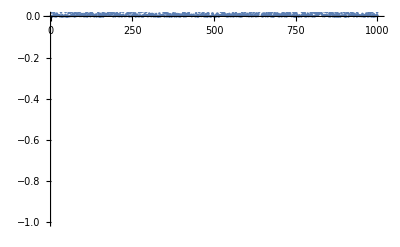

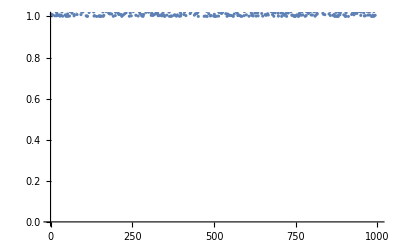

```mathematica
ListPlot[Table[{i,Min[phystest[[i,1]]]},{i,1,Length[cm]}],PlotRange->{-1,0}]
ListPlot[Table[{i,Min[phystest[[i,2]]]},{i,1,Length[cm]}],PlotRange->{-1,0}]
ListPlot[Table[{i,Min[phystest[[i,3]]]},{i,1,Length[cm]}],PlotRange->{0,1}]
```

```mathematica
covmpt=Table[{{a[[i]],0,cp[[i]],0},{0,a[[i]],0,-cm[[i]]},{cp[[i]],0,b[[i]],0},{0,-cm[[i]],0,b[[i]]}},{i,10^3}];
```

```mathematica
phystestt={};
Do[AppendTo[phystestt,{Abs[Eigenvalues[ⅈ Σ . covmpt[[i]]//Chop]]}];,{i,1,Length[covmpt]}]


phystestt[[200]]
```

{{154.94,154.94,0.799213,0.799213}}

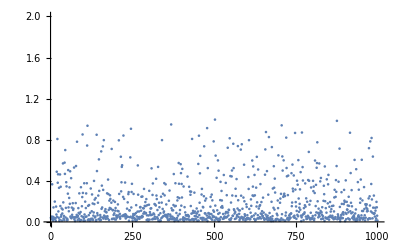

```mathematica
Table[{Min[phystestt[[i,1]]]},{i,1,Length[cm]}];


ListPlot[Table[{i,Min[phystest[[i,1]]]},{i,1,Length[cm]}],PlotRange->{0,2}]
```

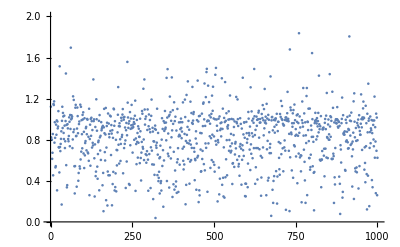

```mathematica
ListPlot[Table[{i,Min[phystestt[[i,1]]]},{i,1,Length[cm]}],PlotRange->{0,2}]
```

```mathematica
Length[phystest]
```

1000

```mathematica
Length[phystestt]
```

1000

```mathematica
Eigenvalues[σ[a,b,cp,cm]+ⅈ Σ]//FullSimplify
```

{1/2 (a+b-√((a-b)^2+2 (2+cm^2+cp^2-√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2)))),1/2 (a+b+√((a-b)^2+2 (2+cm^2+cp^2-√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2)))),1/2 (a+b-√((a-b)^2+2 (2+cm^2+cp^2+√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2)))),1/2 (a+b+√((a-b)^2+2 (2+cm^2+cp^2+√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2))))}

```mathematica
Eigenvalues[ⅈ Σ . σ[a,b,cp,cm]]//FullSimplify
```

{-(ⅈ √(-a^2-b^2-2 cm cp-√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2),(ⅈ √(-a^2-b^2-2 cm cp-√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2),-(ⅈ √(-a^2-b^2-2 cm cp+√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2),(ⅈ √(-a^2-b^2-2 cm cp+√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2)}